# Test Data Trace Plotting

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

( last updated:  Tue 11 Mar 2014 11:44:53 )

( current Git HEAD:  38d18b6f1b9d7c4d8adc19783ea68543ebbeac24 )

( http://github.org/ktakagaki/nounoum )

<<Set JLink` java stack size to 6144Mb>>

```mathematica
ShowJavaConsole[]
```

«JavaObject[com.wolfram.jlink.ui.ConsoleWindow]»

## Load Data

```mathematica
testDataFileDirectory = ParentDirectory[NotebookDirectory[]]<>"\\_testFiles\\Neuralynx"
```

V:\docs\bb\NounouM2\NounouM2\Testing\_testFiles\Neuralynx

```mathematica
testFiles4=FileNames[testDataFileDirectory<>"\\Tet4*.ncs"]
```

{V:\docs\bb\NounouM2\NounouM2\Testing\_testFiles\Neuralynx\Tet4a.ncs,V:\docs\bb\NounouM2\NounouM2\Testing\_testFiles\Neuralynx\Tet4b.ncs,V:\docs\bb\NounouM2\NounouM2\Testing\_testFiles\Neuralynx\Tet4c.ncs,V:\docs\bb\NounouM2\NounouM2\Testing\_testFiles\Neuralynx\Tet4d.ncs}

```mathematica
$NNReader@load[testFiles4]
```

```mathematica
$NNReader@toStringChain[]
```

DataReader LOADED DATA SUMMARY
================================
DataReader( data ch:4, dataAux ch:0, mask: XMask: 0 _masks, events: 0)

     [header  ] XHeaderNull
     [dataORI ] XDataFilterHolder: XData: 4 ch, 3 seg, lengths=Vector(3339264, 123392, 6754816), fs=32000.0)     
          \ XDataFilterDecimate: factor=16     
               \ XDataFilterBuffer: bufferPageLength=16384, garbageQueBound=1024     
                    \ XDataFilterStatistics: 
                    \ XDataFilterFIR: kernel null (off)     
                         \ XDataFilterRMS: halfWindow=100
                    \ XDataFilterMinMaxAbs: halfWindow=100
                    \ XDataFilterFIR: kernel null (off)
     [dataAux ] XDataFilterHolder: XDataNull()
     [mask    ] XMask: 0 _masks
     [events  ] XEventsNull
     [spikes  ] XSpikesNull

## NNTracePlot

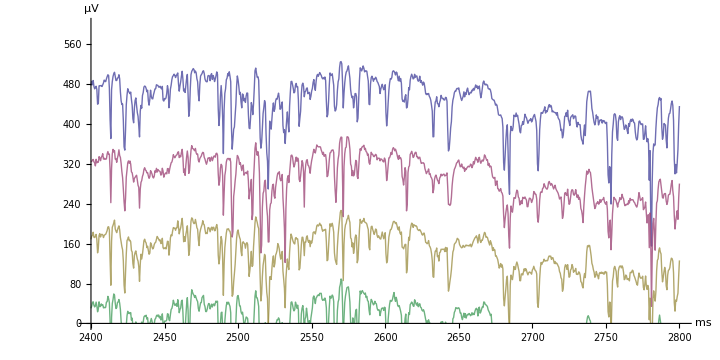

```mathematica
NNTracePlot[$NNReader@data[], Range[0,3],{2400, 2800} , 0, NNStackLists->150]
```

```mathematica
-Graphics-//InputForm
```

Graphics[{}]

```mathematica
$NNReader@data[]@msToFrame[#]& /@ {2400,2800}
```

{4800,5600}

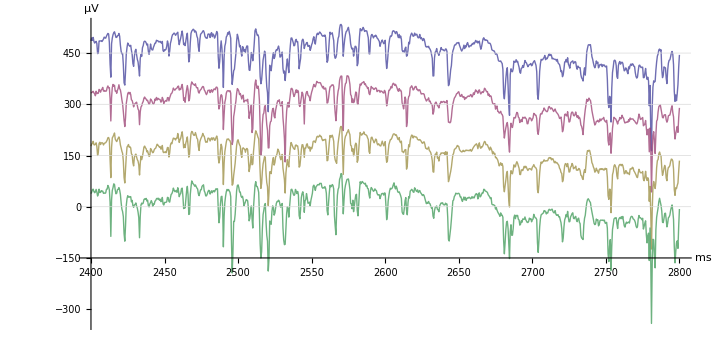

```mathematica
NNTracePlot[$NNReader@data[], Range[0,3],4800;;5600 , 0, NNStackLists->150]
```

```mathematica
$NNReader@data[]@segmentLengths[]@apply[0]
```

208704

```mathematica
$NNReader@data[]@frameToMs[$NNReader@data[]@segmentLengths[]@apply[0]]
```

104352.

```mathematica
Manipulate[
NNTracePlot[$NNReader@data[], Range[0,3],{x, x+400}, 0, NNStackLists->150],
{x, 0,103500}
]
```

NNTracePlot::invalidArgs: Function called with invalid arguments « JavaObject[nounou.data.filters.XDataFilterFIR] »{0, 1, 2, 3}{180000, 180800, 1}00TruemsμV1True.

NNTracePlot::invalidArgs: Function called with invalid arguments « JavaObject[nounou.data.filters.XDataFilterFIR] »{0, 1, 2, 3}{180000, 180800, 1}0150TruemsμV1True.

```mathematica
$NNReader@data[]@segmentLengths[]@apply[0]
```

208704